## Rutina para calcular los campos - fase en 3 dimensiones Definiendo el campo fase ϕ :

```mathematica
Nx = 60;
Ny = 40;
Nz = 40;
R = 11;
```

```mathematica
ϕ0[x_,y_,z_]=-Tanh[Sqrt[(x-Nx/2)^2 + (y - Ny/2)^2 + (z)^2]-R];
```

```mathematica
ϕ0[Nx/2,Ny/2,z]
```

Tanh[11-√(z^2)]

```mathematica
ContourPlot3D[ϕ0[x,y,z]==0,{x,0,Nx},{y,0,Ny},{z,0,Nz},AxesLabel->{Style["x",Bold,15],Style["y",Bold,15],Style["z",Bold,15]},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
a = Min[Table[Abs[ϕ0[Nx/2,Ny/2,z]],{z,0,Nz}]];
```

```mathematica
R1 = Flatten[Position[Table[Abs[ϕ0[Nx/2,Ny/2,z]],{z,0,Nz}],a]]//First
```

12

```mathematica
u[x_,y_,z_]=1+3.5*Exp[-((x-Nx/2)^2 + (y-Ny/2)^2 + (z-R1+8)^2)/100]
```

1+3.5 ⅇ^(1/100 (-(-30+x)^2-(-20+y)^2-(8-R1+z)^2))

```mathematica
ContourPlot3D[u[x,y,z],{x,0,Nx},{y,0,Ny},{z,0,Nz},AxesLabel->{Style["x",Bold,15],Style["y",Bold,15],Style["z",Bold,15]},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
Φ[x_,y_,z_,t_,C0_,ϵ_]=-ϕ[x,y,z,t]+ϕ[x,y,z,t]^3-C0*ϵ^2*(1-ϕ[x,y,z,t]^2)
```

-ϕ[x,y,z,t]+ϕ[x,y,z,t]^3-C0 ϵ^2 (1-ϕ[x,y,z,t]^2)

```mathematica
F[x_,y_,z_,t_,C0_,ϵ_,As_,umin_,umax_,ufar_,Af_,Ab_]=2*Ab*Φ[x,y,z,t,C0,ϵ]*(3*ϕ[x,y,z,t]^2 -1-2*C0*ϵ*ϕ[x,y,z,t]) + 4*As*ϕ[x,y,z,t]*(ϕ[x,y,z,t]^2 -1)*(u[x,y,z]-umin)^2*(u[x,y,z]-umax)^2 +2*Af*ϕ[x,y,z,t]*(u[x,y,z]-ufar)^2 -2Ab*ϵ^2 *(D[Φ[x,y,z,t,C0,ϵ],x,x]+D[Φ[x,y,z,t,C0,ϵ],y,y]+D[Φ[x,y,z,t,C0,ϵ],z,z])
```

2 Af (1+3.5 ⅇ^(1/100 (-(-30+x)^2-(-20+y)^2-(-4+z)^2))-ufar)^2 ϕ[x,y,z,t]+4 As (1+3.5 ⅇ^(1/100 (-(-30+x)^2-(-20+y)^2-(-4+z)^2))-umax)^2 (1+3.5 ⅇ^(1/100 (-(-30+x)^2-(-20+y)^2-(-4+z)^2))-umin)^2 ϕ[x,y,z,t] (-1+ϕ[x,y,z,t]^2)+2 Ab (-1-2 C0 ϵ ϕ[x,y,z,t]+3 ϕ[x,y,z,t]^2) (-ϕ[x,y,z,t]+ϕ[x,y,z,t]^3-C0 ϵ^2 (1-ϕ[x,y,z,t]^2))-2 Ab ϵ^2 (2 C0 ϵ^2 (ϕ^(0,0,1,0)[x,y,z,t])^2+6 ϕ[x,y,z,t] (ϕ^(0,0,1,0)[x,y,z,t])^2-ϕ^(0,0,2,0)[x,y,z,t]+2 C0 ϵ^2 ϕ[x,y,z,t] ϕ^(0,0,2,0)[x,y,z,t]+3 ϕ[x,y,z,t]^2 ϕ^(0,0,2,0)[x,y,z,t]+2 C0 ϵ^2 (ϕ^(0,1,0,0)[x,y,z,t])^2+6 ϕ[x,y,z,t] (ϕ^(0,1,0,0)[x,y,z,t])^2-ϕ^(0,2,0,0)[x,y,z,t]+2 C0 ϵ^2 ϕ[x,y,z,t] ϕ^(0,2,0,0)[x,y,z,t]+3 ϕ[x,y,z,t]^2 ϕ^(0,2,0,0)[x,y,z,t]+2 C0 ϵ^2 (ϕ^(1,0,0,0)[x,y,z,t])^2+6 ϕ[x,y,z,t] (ϕ^(1,0,0,0)[x,y,z,t])^2-ϕ^(2,0,0,0)[x,y,z,t]+2 C0 ϵ^2 ϕ[x,y,z,t] ϕ^(2,0,0,0)[x,y,z,t]+3 ϕ[x,y,z,t]^2 ϕ^(2,0,0,0)[x,y,z,t])

```mathematica
Fs[x_,y_,z_,t_,σ_]=-2*σ*(D[ϕ[x,y,z,t],x,x]+D[ϕ[x,y,z,t],y,y]+D[ϕ[x,y,z,t],z,z])
```

-2 σ (ϕ^(0,0,2,0)[x,y,z,t]+ϕ^(0,2,0,0)[x,y,z,t]+ϕ^(2,0,0,0)[x,y,z,t])

```mathematica
Ω[x_,y_,z_,t_]= F[x,y,z,t,0.1,2,2,0,1,0,2,1]+Fs[x,y,z,t,0.1]
```

```mathematica
NDSolve[{D[ϕ[x,y,z,t],t]==D[Ω[x,y,z,t],x,x]+D[Ω[x,y,z,t],y,y]+D[Ω[x,y,z,t],z,z],D[ϕ[0,y,z,t],x,x]==0,D[ϕ[Nx,y,z,t],x,x]==0,D[ϕ[x,0,z,t],y,y]==0,D[ϕ[x,Ny,z,t],y,y]==0,D[ϕ[x,y,0,t],z,z]==0,D[ϕ[x,y,Nz,t],z,z]==0,ϕ[0,y,z,t]==ϕ[1,y,z,t],ϕ[Nx,y,z,t]==ϕ[Nx-1,y,z,t],ϕ[x,0,z,t]==ϕ[x,1,z,t],ϕ[x,Ny,z,t]==ϕ[x,Ny-1,z,t],ϕ[x,y,0,t]==ϕ[x,y,1,t],ϕ[x,y,Nz,t]==ϕ[x,y,Nz-1,t],ϕ[x,y,z,0]==ϕ0[x,y,z]},ϕ,{x,0,Nx},{y,0,Ny},{z,0,Nz},{t,0,2}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[TrueTrueTrue« 12 »ϕ[x, 40, z] == ϕ[« 1 »]ϕ[x, y, 0] == ϕ[x, y, 1]ϕ[x, y, 40] == ϕ[x, y, 39]ϕ[x, y, z, 0] == Tanh[11 - √Power[« 2 »] + Power[« 2 »] + Power[« 2 »]].

```mathematica
test=NDSolve[{D[f[t,x],t]==D[f[t,x],x,x],f[0,x]==0,f[t,0]==Sin[t],f[t,5]==0},f,{t,0,10},{x,0,5}]
```

{{f→InterpolatingFunction[{{0., 10.}, {0., 5.}}, <>]}}

```mathematica
Dimensions[f[t,x]]
```

{2}

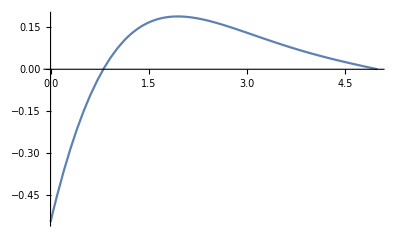

```mathematica
Plot[f[10,x]/.test,{x,0,5},PlotRange->All]
```

```mathematica
Plot3D[Evaluate[f[t,x]/.test],{t,0,10},{x,0,5}, PlotRange->All]
```

-Graphics3D-

```mathematica
FullSimplify[ϕ0[0,0,0]]
```

Tanh[11-10 √13]

```mathematica
μ=-0.8(1-ϕ[x,y,z,t]^2);
```

```mathematica
F1 = 3.2*μ*ϕ[x,y,z,t];
```

```mathematica
NDSolve[{D[ϕ[x,y,z,t],t]==Laplacian[F1,{x,y,z}]+NeumannValue[0,True],ϕ[x,y,z,0]==ϕ0[x,y,z]},ϕ,{x,0,Nx},{y,0,Ny},{z,0,Nz},{t,0,1}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

NDSolve[{ϕ^(0,0,0,1)[x,y,z,t]==NeumannValue[0,True]+15.36 ϕ[x,y,z,t] (ϕ^(0,0,1,0)[x,y,z,t])^2+5.12 ϕ[x,y,z,t]^2 ϕ^(0,0,2,0)[x,y,z,t]-2.56 (1-ϕ[x,y,z,t]^2) ϕ^(0,0,2,0)[x,y,z,t]+15.36 ϕ[x,y,z,t] (ϕ^(0,1,0,0)[x,y,z,t])^2+5.12 ϕ[x,y,z,t]^2 ϕ^(0,2,0,0)[x,y,z,t]-2.56 (1-ϕ[x,y,z,t]^2) ϕ^(0,2,0,0)[x,y,z,t]+15.36 ϕ[x,y,z,t] (ϕ^(1,0,0,0)[x,y,z,t])^2+5.12 ϕ[x,y,z,t]^2 ϕ^(2,0,0,0)[x,y,z,t]-2.56 (1-ϕ[x,y,z,t]^2) ϕ^(2,0,0,0)[x,y,z,t],ϕ[x,y,z,0]==Tanh[11-√((-30+x)^2+(-20+y)^2+z^2)]},ϕ,{x,0,60},{y,0,40},{z,0,40},{t,0,1}]

```mathematica
ContourPlot3D[ϕ[x,y,z,0.005]/.%,{x,0,Nx},{y,0,Ny},{z,0,Nz}]
```

$Aborted

```mathematica
Plot[-1+Exp[-1000 t],{t,-0.1,0.2}]
```

-Graphics-